### Wprowadzenie wzorow na sile odsrodkowa "F_od" i sile grawitacji "F_g".

```mathematica
ClearAll["Global`*"];
Fod=(m×v^2)/R;
Fg=m×g;
```

### Wprowadzenie wzorow na energie potencjalne wozka w punkcie startu "E_p1" i w najwyzszym punkcie petli "E_p2" oraz na energie kinetyczna wozka w najwyzszym punkcie petli "E_k2". Symbol "m" oznacza mase wozka wraz z pasazerami, "g" - przyspieszenie ziemskie, "v" - predkosc wozka.

```mathematica
Ep1=m×g×H;
Ep2=m×g×(2×R);
Ek2=(m×v^2)/2;
```

### Rozwiazanie ukladu rownan bedacych matematycznym zapisem rownosci sily odsrodkowej i sily przyciagania ziemskiego w najwyzszym punkcie petli oraz zasady zachowania energii.

```mathematica
r1=Solve[{Fod==Fg, Ep1-Ep2==Ek2},{H,v}]
```

{{H→(5 R)/2,v→-√g √R},{H→(5 R)/2,v→√g √R}}

### Sporzadzenie wykresu obrazujacego zaleznosc wymaganej wysokosci zjezdzalni "H" od promienia petli "R".

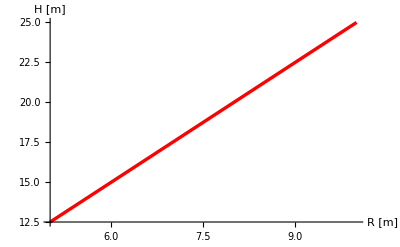

```mathematica
Plot[H/.r1[[1,1]],{R,5,10},
TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"R [m]","H [m]"}]
```